```mathematica
Clear["Global`*"]
```

```mathematica
(* Probabilities that the donor is good given observations. Oij is the probability that the donor is good given the observation of a recipient doing action i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. Specifically, Ocg=P(good|->G), Ocb=P(good|->B), Odg=P(good|¬->G), and Odb=P(good|¬->B). *)
Ocg=ϵ*g/(ϵ*g+e*(1-g));
Ocb=Ocg;
Odg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Odb=Odg;
```

```mathematica
(* Probabilities that a donor is good given their intention. Iij is the probability that the donor is good given their intention i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. *)
Icg= ϵ*Ocg + (1-ϵ)*Odg;
Icb= Icg;
Idg= (1-e)*Odg + e*Ocg;
Idb= Idg;
```

```mathematica
(* Changes in reputations for gx, gy, and gz *)
gxplus=(1-gx)*Icg/.{g-> x*gx+y*gy+z*gz};
gxminus=gx*(1-Icg)/.{g-> x*gx+y*gy+z*gz};
gyplus=(1-gy)*Idg/.{g-> x*gx+y*gy+z*gz};
gyminus=gy*(1-Idg)/.{g-> x*gx+y*gy+z*gz};
gzplus=(1-gz)*(Icg*(x*gx+y*gy+z*gz)+Idg*(x*(1-gx)+y*(1-gy)+z*(1-gz)))/.{g-> x*gx+y*gy+z*gz};
gzminus=gz*((1-Icg)*(x*gx+y*gy+z*gz)+(1-Idg)*(x*(1-gx)+y*(1-gy)+z*(1-gz)))/.{g-> x*gx+y*gy+z*gz};
Δgx=gxplus-gxminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
Δgy=gyplus-gyminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
Δgz=gzplus-gzminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
(*Solve[gxplus==gxminus&&gyplus==gyminus&&gzplus==gzminus,{gx,gy,gz}]*)
(*{{Gx,Gy,Gz}}=Values[Solve[gxplus==gxminus&&gyplus==gyminus&&gzplus==gzminus,{gx,gy,gz}]]/.{x->x[t],y->y[t],z->z[t]}*)
```

```mathematica
(* The replicator equations *)
Px=r*(x[t]+z[t]*gx[t])-1;
Py=r*(x[t]+z[t]*gy[t]);
Pz=r*(x[t]+z[t]*gz[t])-x[t]*gx[t]-y[t]*gy[t]-z[t]*gz[t];
Pbar=x[t]*Px+y[t]*Py+z[t]*Pz;
xdot=x[t]*(Px-Pbar);
ydot=y[t]*(Py-Pbar);
zdot=z[t]*(Pz-Pbar);
```

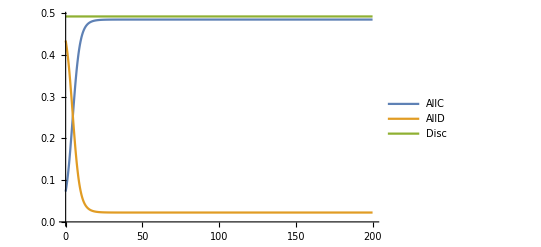

```mathematica
(* Plot numerical solutions *)
params={τ-> 100000,r->3,ϵ->(1-e1)*(1-e2)+e1*e2,e->e2,e1->0.01,e2->0.01};
eqns={x'[t]==xdot,y'[t]==ydot,z'[t]==zdot,gx'[t]==τ*Δgx,gy'[t]==τ*Δgy,gz'[t]==τ*Δgz}//.params;
rand1=RandomReal[];
rand2=RandomReal[];
rand3=RandomReal[];
x0=rand1/(rand1+rand2+rand3);
y0=rand2/(rand1+rand2+rand3);
z0=rand3/(rand1+rand2+rand3);
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
IC={x[0]==x0,y[0]==y0,z[0]==z0,gx[0]==gx0,gy[0]==gy0,gz[0]== gz0};
sol=NDSolve[Join[eqns,IC],{x,y,z,gx,gy,gz},{t,0,200}];
Plot[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,200},PlotLegends->{"AllC","AllD","Disc"}]
```

```mathematica
nsoleq={0==xdot,0==ydot,0==zdot,0==Δgx,0==Δgy,0==Δgz};
conds={0≤ x≤ 1,0≤y≤ 1,0≤z≤ 1,x+y+z==1,0≤gx≤ 1,0≤gy≤ 1,0≤gz≤ 1}
nsol=NSolve[Join[nsoleq,conds]/.{x[t]->x,y[t]->y,z[t]->z,gx[t]->gx,gy[t]->gy,gz[t]->gz},{x,y,z,gx,gy,gz},Reals]
```

{0≤x≤1,0≤y≤1,0≤z≤1,x+y+z==1,0≤gx≤1,0≤gy≤1,0≤gz≤1}

$Aborted